```mathematica
407-107-196
```

104

```mathematica
NotebookDirectory[]
```

/Users/yongdou/Dropbox/magnetic roller/

```mathematica
ClearAll["Global`*"]
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
data = Import[NotebookDirectory[]<>"SpherePlaneResistance.txt","Table"];
ξdata=data[[All,1]];
XAdata=data[[All,2]];
YAdata=data[[All,3]];
YBdata=data[[All,4]];
XCdata=data[[All,5]];
YCdata=data[[All,6]];
δ=0.01;
YAVal=Interpolation[Transpose[{ξdata,YAdata}]][δ];
YBVal=Interpolation[Transpose[{ξdata,YBdata}]][δ];
YCVal=Interpolation[Transpose[{ξdata,YCdata}]][δ];
XAVal=Interpolation[Transpose[{ξdata,XAdata}]][δ];
XCVal=Interpolation[Transpose[{ξdata,XCdata}]][δ];
AA={{YAVal,0,0},{0,YAVal,0},{0,0,XAVal}};
BB={{0,YBVal,0},{-YBVal,0,0},{0,0,0}};
CC={{YCVal,0,0},{0,YCVal,0},{0,0,XCVal}};
Resistance=ArrayFlatten[ {{AA,Transpose[BB]},{BB,CC}}];
```

## ## construct function based on the main frequency

```mathematica
MA={{Cos[(2 π)/m],-Sin[(2 π)/m],0},
{Sin[(2 π)/m], Cos[(2 π)/m],0},
{0,0,1}};
MS=IdentityMatrix[3] Sin[(2 n π)/m];
MC=IdentityMatrix[3] Cos[(2 n π)/m];
M=ArrayFlatten[{{MA-MC,MS},{-MS,MA-MC}}];
NullSpace[M/.{m->8,n->1}]
NullSpace[M/.{m->8,n->2}]
NullSpace[M/.{m->8,n->3}]
NullSpace[M/.{m->8,n->4}]
NullSpace[M/.{m->8,n->5}]
NullSpace[M/.{m->8,n->6}]
NullSpace[M/.{m->8,n->7}]
NullSpace[M/.{m->8,n->8}]
NullSpace[M/.{m->8,n->9}]
```

{{-1,0,0,0,1,0},{0,1,0,1,0,0}}

{}

{}

{}

«2 more identical outputs»

{{1,0,0,0,1,0},{0,-1,0,1,0,0}}

{{0,0,0,0,0,1},{0,0,1,0,0,0}}

{{-1,0,0,0,1,0},{0,1,0,1,0,0}}

```mathematica
RotationMatrix[-45 Degree,{1,0,0}].{0,1,0 }
```

{0,1/(√2),-1/(√2)}

```mathematica
Clear[B]
n=6;
(*ω=0.02;*)
ω1=0.35

B[{v1_,v2_,v3_,v4_,v5_,v6_,v7_,ω_},t_]:=RotationMatrix[-10Degree,{1,0,0}].(v1({-1,0,0}Cos[ ω t]+{0,1,0}Sin[ω t])+
v2({1,0,0}Cos[(n-1) ω t]+{0,1,0}Sin[(n-1) ω t])+
v3({0,-1,0} Cos[(n-1)  ω t]+{1,0,0}Sin[(n-1) ω t])+
v4({0,0,1}Sin[n ω t])+
v5({0,0,1}Cos[n ω t])+
v6({-1,0,0} Cos[(n+1) ω t]+{0,1,0}Sin[(n+1) ω t])+
v7({0,1,0} Cos[(n+1) ω t]+{1,0,0}Sin[(n+1) ω t]))
Bflat[{v1_,v2_,v3_,v4_,v5_,v6_,v7_,ω_},t_]:=(v1({-1,0,0}Cos[ ω t]+{0,1,0}Sin[ω t])+
v2({1,0,0}Cos[(n-1) ω t]+{0,1,0}Sin[(n-1) ω t])+
v3({0,-1,0} Cos[(n-1)  ω t]+{1,0,0}Sin[(n-1) ω t])+
v4({0,0,1}Sin[n ω t])+
v5({0,0,1}Cos[n ω t])+
v6({-1,0,0} Cos[(n+1) ω t]+{0,1,0}Sin[(n+1) ω t])+
v7({0,1,0} Cos[(n+1) ω t]+{1,0,0}Sin[(n+1) ω t]))
(*B[{v1_,v2_,v3_,v4_,v5_,v6_,v7_,ω_},t_]:=RotationMatrix[-10 Degree,{1,0,0}].{Cos[ω1 t] Sin[ω1/10 t],Cos[ω1 t] Cos[ω1/10 t],Sin[ω1 t]}
Bflat[{v1_,v2_,v3_,v4_,v5_,v6_,v7_,ω_},t_]:={Cos[ω1 t] Cos[ω1/10 t],Cos[ω1 t] Sin[ω1/10 t],Sin[ω1 t]}*)
```

0.35

```mathematica
roller[{v1_,v2_,v3_,v4_,v5_,v6_,v7_,ω_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={v1,v2,v3,v4,v5,v6,v7,ω};
tMax = (*Min[200 2 π/parameter[[1]],50000.0]*0+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,100}   ];
Lq=Simplify[Cross[mq,B[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]
rollerflat[{v1_,v2_,v3_,v4_,v5_,v6_,v7_,ω_}]:=Module[{parameter,tMax,Rq,mq,Lq,F,FLq,UΩq,Uq,Ωq,Q,quaternionRate,
q,ϕ,θ,ψ,qIC,para,sol,data,dct,tdata},
parameter={v1,v2,v3,v4,v5,v6,v7,ω};
tMax =(* Min[200 2 π/parameter[[1]],50000.0]+*)5000;
(*first field is magnetic , second is gravity*)

Rq={{q0^2+q1^2-q2^2-q3^2,2q1 q2+2q0 q3,2q1 q3-2q0 q2},
{2q1 q2-2q0 q3,q0^2-q1^2+q2^2-q3^2,2q2 q3+2q0 q1},
{2 q1 q3+2 q0 q2,2q2 q3-2 q0 q1, q0^2-q1^2-q2^2+q3^2}};
(*magnetic moment*)
mq=Simplify[Transpose[Rq] .{0,0,1}   ];
Lq=Simplify[Cross[mq,Bflat[parameter,t    ]   ]];
(*force *)
F ={0 ,0,0};
FLq=ArrayFlatten[{F,Lq},1];
UΩq=Simplify[Inverse[Resistance].FLq];
Uq=UΩq[[1;;3]];
Ωq=UΩq[[4;;6]];
Q ={{q0 ,-q1,-q2,-q3},
{q1,q0,q3,-q2},
{q2,-q3,q0,q1},
{q3,q2,-q1,q0}};
(*equation 156*)
quaternionRate=1/2 Q.ArrayFlatten[{{0},Ωq},1];
q={Cos[ϕ/2]Cos[θ/2]Cos[ψ/2]-Sin[ϕ/2]Cos[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Cos[ψ/2]+Sin[ϕ/2]Sin[θ/2]Sin[ψ/2],
Cos[ϕ/2]Sin[θ/2]Sin[ψ/2]-Sin[ϕ/2]Sin[θ/2]Cos[ψ/2],
Cos[ϕ/2]Cos[θ/2]Sin[ψ/2]+Sin[ϕ/2]Cos[θ/2]Cos[ψ/2]};
qIC = q/.{ϕ->RandomReal[2 π],θ->RandomReal[2 π],ψ->RandomReal[2 π]};
para={q0->q0[t],q1->q1[t],q2->q2[t],q3->q3[t]};
sol=NDSolve[{
q0'[t]==(quaternionRate[[1]]/.para),
q1'[t]==(quaternionRate[[2]]/.para),
q2'[t]==(quaternionRate[[3]]/.para),
q3'[t]==(quaternionRate[[4]]/.para),
x'[t]==(Uq[[1]]/.para),
y'[t]==(Uq[[2]]/.para),
q0[0]==qIC[[1]],
q1[0]==qIC[[2]],
q2[0]==qIC[[3]],
q3[0]==qIC[[4]],
x[0]==0,
y[0]==0},
{q0[t],q1[t],q2[t],q3[t],x[t],y[t]},{t,0,tMax}];
(*data=Table[x[t]/.sol[[1]],{t,0,4000,1}];
dct=FourierDCT[data];
  tdata=FourierDCT[PadRight[Take[dct,2],4000,0],3];*)
(*Mean[D[y[t]/.sol[[1]],t]/.t->Table[i,{i,tMax 0.5,tMax}]]*)
(*y[t]/.sol[[1]]/.t->Table[i,{i,200 2 π/ω1 0.5,200 2 π/ω1 0.75,1}];
200 2 π/ω1 0.75*)
(*data1=Table[{t/(  2 π/ω2),x[t]/.sol[[1]]},{t,0,4000,1}];
data2=Table[{t/(2 π /ω2),y[t]/.sol[[1]]},{t,0,4000,1}];
lm1=LinearModelFit[MovingAverage[data1,Round[      2 π/ω2]],x,x];
lm2=LinearModelFit[MovingAverage[data2,Round[      2 π/ω2]],x,x];
{sol,lm1["BestFitParameters"][[2]],lm2["BestFitParameters"][[2]]}*)
sol
]


(*B[{ω1_,ω2_,ω3_,ω4_,A1_,A2_,A3_,B1_, B2_},t_]*)
```

```mathematica
optimize[{v1_,v2_,v3_,v4_,v5_,v6_,v7_},ω_]:=Module[{sol1,sol2,dy,dx,can},
can={};
sol1=roller[{v1,v2,v3,v4,v5,v6,v7,ω}];
sol2=rollerflat[{v1,v2,v3,v4,v5,v6,v7,ω}];
dx=((x[t]/.sol1[[1]])-(x[t]/.sol2[[1]]))/.t->5000  ;
dy=((y[t]/.sol1[[1]])-(y[t]/.sol2[[1]]))/.t->5000;
If[(dy>0)&&(Abs[dy/dx]>4),can= {{v1,v2,v3,v4,v5,v6,v7,ω},{dy,dx}} ];
can
]
```

```mathematica
optimize1[{v1_,v2_,v3_,v4_,v5_,v6_,v7_},ω_]:=Module[{sol1,sol2,dy,dx,can},
can={};
sol1=roller[{v1,v2,v3,v4,v5,v6,v7,ω}];
dy=-(y[t]/.sol1[[1]]/.t->10)+  (y[t]/.sol1[[1]]/.t->(10+2 π/0.01 *7)) ;
dx=-(x[t]/.sol1[[1]]/.t->10)+  (x[t]/.sol1[[1]]/.t->(10+2 π/0.01 *7));
If[(dy>0)&&(Abs[dy/dx]>2),can= {{v1,v2,v3,v4,v5,v6,v7,ω},{dy,dx}} ];
can
]
```

```mathematica
search[{v1_,v2_,v3_,v4_,v5_,v6_,v7_},ω_]:=Module[{sol1,sol2,dy,dx,can},
can={};
sol1=roller[{v1,v2,v3,v4,v5,v6,v7,ω}];
dy=-(y[t]/.sol1[[1]]/.t->10)+  (y[t]/.sol1[[1]]/.t->(10+2 π/0.01 *7)) ;
dx=-(x[t]/.sol1[[1]]/.t->10)+  (x[t]/.sol1[[1]]/.t->(10+2 π/0.01 *7));
Abs[dy/dx]*Sign[dy]
]
```

```mathematica
hp=ToExpression[Import[NotebookDirectory[]<>"numercal_hp.csv"]];
```

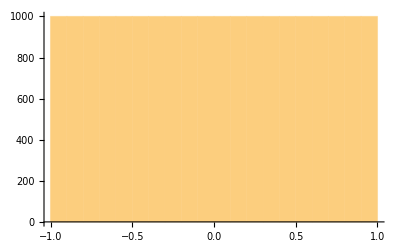

```mathematica
Histogram[hp[[All,1]]]
```

```mathematica
Dimensions[hp]
```

{20000,7}

```mathematica
data6=ParallelTable[search[ hp[[i]]          ,0.01],{i,1,20000}]
```

{-0.000821958,0.00236929,0.00289527,0.00652499,0.135082,-0.0119658,-0.0103659,0.00257189,0.00299505,-0.000165248,-0.00155579,1.09814,0.0097316,19974,-0.000725753,0.00465299,-0.000130819,-0.0000707978,-0.00821392,0.000278196,-0.000388056,0.0164161,-0.000269229,0.0128155,-0.0109122,0.00640713,-0.00195195}
 |  |  |  |

```mathematica
data7=ParallelTable[optimize1[RandomReal[{-1,1},7],0.01],{i,1,10000}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},9796,{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}
 |  |  |  |

```mathematica
data7=Select[data7,UnsameQ[#,{}]&]
```

```mathematica
data7={{{-0.5759277842420132,-0.7751303674403065,-0.7210199711658811,0.13468251276599297,-0.46975920482958466,0.38118169040801364,0.5035092504516023,0.01},{0.3056129050323587,-0.010258224236399993}},{{-0.36181567881385135,0.5348852068452916,0.8682938152534634,-0.9577348017524829,0.37629340942215395,0.6700301844484269,-0.584807498771132,0.01},{0.0009262573582018707,0.0002672473495846546}},{{-0.2346328974485954,-0.5370455859338183,-0.34245652209930855,0.14031574641776956,0.41097206526755947,0.4609133677252144,0.40106918657867174,0.01},{0.02252518749523126,-0.0052190393844997185}},{{-0.735741011430366,-0.2573158737570851,-0.4602354196483187,-0.5468348800991563,-0.11808243486309689,0.4753382795016976,-0.09223327784098068,0.01},{0.0018947358744333676,0.00044762292139919474}}}
```

{{{-0.575928,-0.77513,-0.72102,0.134683,-0.469759,0.381182,0.503509,0.01},{0.305613,-0.0102582}},{{-0.361816,0.534885,0.868294,-0.957735,0.376293,0.67003,-0.584807,0.01},{0.000926257,0.000267247}},{{-0.234633,-0.537046,-0.342457,0.140316,0.410972,0.460913,0.401069,0.01},{0.0225252,-0.00521904}},{{-0.735741,-0.257316,-0.460235,-0.546835,-0.118082,0.475338,-0.0922333,0.01},{0.00189474,0.000447623}}}

```mathematica
Export[NotebookDirectory[]<>"hp_6fold.csv",data6]
```

/Users/yongdou/Dropbox/magnetic roller/hp_6fold.csv

```mathematica
data7=ToExpression[Import[NotebookDirectory[]<>"numerical7fold.csv"]];
```

```mathematica
NotebookDirectory
```

NotebookDirectory

```mathematica
{7,2}
```

{7,2}

```mathematica
number=2
data7[[number,1]]
sol1=rollerflat[data7[[number,1]]];
sol2=roller[data7[[number,1]]];
para=data7[[number]][[1]]
```

2

{-0.361816,0.534885,0.868294,-0.957735,0.376293,0.67003,-0.584807,0.01}

{-0.361816,0.534885,0.868294,-0.957735,0.376293,0.67003,-0.584807,0.01}

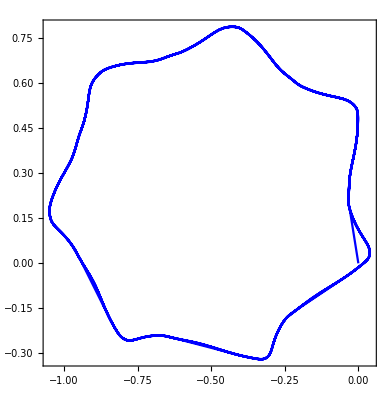

```mathematica
Show[
ParametricPlot[{x[t]/.sol2[[1]],y[t]/.sol2[[1]]},{t,0,5000},Frame->True,AspectRatio->Equal,PlotStyle->{Blue}]

]
```

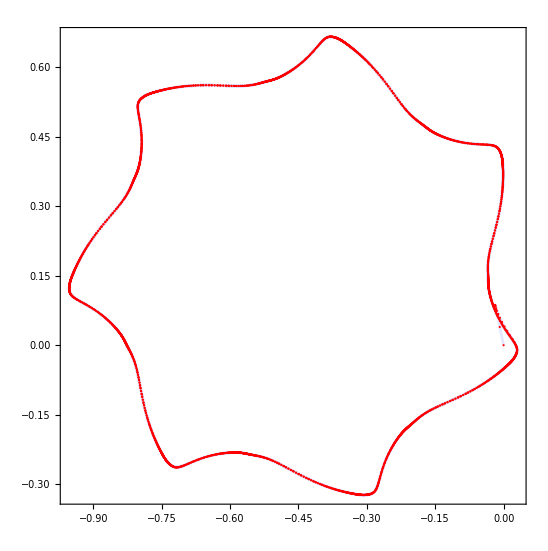

```mathematica
Show[
ParametricPlot[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,5000},Frame->True,AspectRatio->Equal,PlotStyle->{Blue,Opacity[0.1],AbsoluteThickness[2]}],
ListPlot[Table[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,5000,1}],Frame->True,AspectRatio->Equal,PlotStyle->{Large,Red}]

]
```

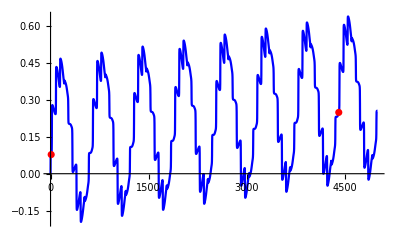

```mathematica
Show[
Plot[{y[t]/.sol1[[1]]},{t,0,5000},PlotStyle->{Blue}],
ListPlot[{{10+7*2π/0.01,y[t]/.sol1[[1]]/.t->(10+7*2π/0.01)},{10,y[t]/.sol1[[1]]/.t->(10)}},PlotStyle->Red]

]
```

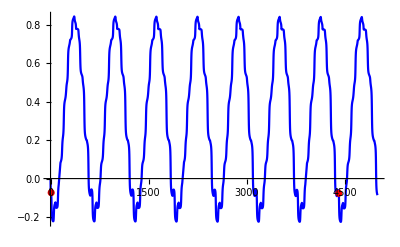

{-0.185076,-0.632476,-0.814134,-0.0212693,0.0349922,0.900341,-0.436197,0.01}

```mathematica
Show[
Plot[{x[t]/.sol1[[1]]},{t,0,5000},PlotStyle->{Blue}],
ListPlot[{{10+7*2π/0.01,x[t]/.sol1[[1]]/.t->(10+7*2π/0.01)},{10,x[t]/.sol1[[1]]/.t->(10)}},PlotStyle->Red]

]
```

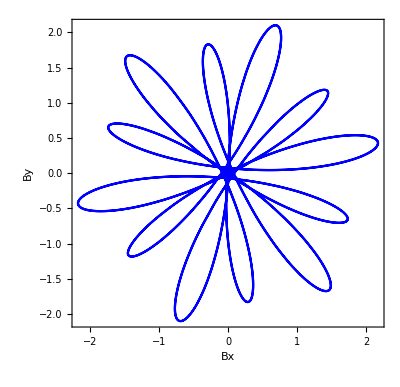

```mathematica
ParametricPlot[Bflat[para,t][[1;;2]],{t,0,400 π},PlotStyle->Blue,Frame->True,FrameLabel->{Bx,By}]
```

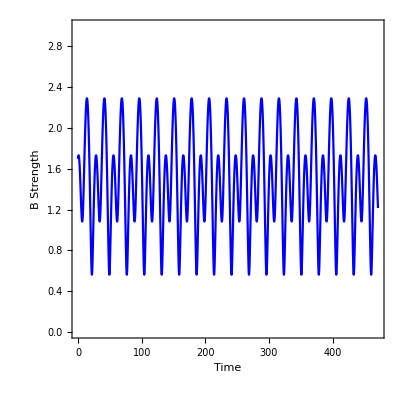

```mathematica
Plot[Norm[Bflat[para,t][[1;;3]]],{t,0,150π},PlotRange->{0,3},PlotStyle->Blue,Frame->True, FrameLabel->{"Time", "B Strength"},AspectRatio->1]
```

```mathematica
ParametricPlot3D[Bflat[para,t],{t,0,400 π},PlotStyle->Blue,AxesLabel->{"BX","BY","BZ"},AspectRatio->Equal,ColorFunction->"DarkRainbow"]
```

-Graphics3D-

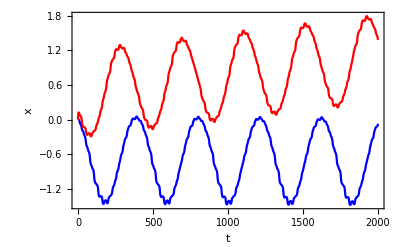

```mathematica
Plot[{x[t]/.sol1[[1]],y[t]/.sol1[[1]]},{t,0,2000},Frame->True,PlotStyle->{Blue,Red},FrameLabel->{"t","x"}]
```

```mathematica
Export["can_0106_01.csv",can]
```

```mathematica
990000 0.01/12
```

825.

```mathematica
45 1.4
```

63.

```mathematica
120000/12.0 0.3
```

3000.

```mathematica
5200 0.3
```

1560.

```mathematica
1900/2 3
```

2850

```mathematica
3100 0.6
```

1860.

```mathematica
58 12*577/393 1.0
```

```mathematica
1021.8625954198473/(163+97)
```

3.93024

```mathematica
1000*12+75000
```

87000

```mathematica
120000
```

12000.

```mathematica
75000*0.03
```

```mathematica
(12000-2250.)/12
```

812.5

```mathematica
2*5*2*2*4+2*5*2*2*4/2 1.5
```

280.

```mathematica
200/ (2 π) 1.0
```

31.831

```mathematica
(3.556 45+3.8383 30)/75
```

3.66892

```mathematica
(9.25-8.875)/100
```

```mathematica
0.00375 120000
```

450.

```mathematica
80000/13476.0
```

5.93648